```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/cmishra/Projects/BaryonsFromMesons/NatureSubmission/Baryons-from-Mesons-ML-master

```mathematica
(*general*)
MeanStdExpScale[μ_,σ_]:=Return[{Exp[μ+σ^2/2],Exp[2μ+σ^2](Exp[σ^2]-1)}]
BoundsExpScale[μ_,σ_]:=Return[{Exp[μ+σ^2/2],(Exp[2μ+σ^2](Exp[σ^2]-1))^(1/2)}]
ExpMean[μ_,σ_]:=Exp[μ+σ^2/2];
ExpMeans[μs_,σs_]:=Table[Exp[μs[[i]]+σs[[i]]^2/2],{i,Length[μs]}];
TR[a_,b_]:=Thread[Rule[a,b]];
DD:=DeleteDuplicates;
NN[x_]:=N[x,20];

MeanErrors[preds_,true_]:=Module[{X},
(* returns mean absolute error and standard deviation of absolute error *)
X=Abs[(preds-true)/true];
Return[{Mean[X],StandardDeviation[X]}]];

TakeMean[x_]:=If[Length[x]>0,Return[x[[1]]],Return[x]](* for numbers of the form Around *)

MM[l_List]:=Module[{p,r,pr},If[MatrixQ[l],Return[l//MatrixForm],p=Position[l,_?MatrixQ,Infinity];
r=Map[MatrixForm,Cases[l,_?MatrixQ,Infinity]];
pr=Table[p[[i]]->r[[i]],{i,1,Length[p]}];
ReplacePart[l,pr]]];

ErrorsNatStd[trues_,μs_,σs_]:=Total[100*(Abs[Exp[trues]-ExpMeans[μs,σs]]/Exp[trues])]/Length[trues];

ListAllErrors[Mtrue_,Btrue_,Etrue_,Mmean_,Bmean_,Emean_,Mstd_,Bstd_,Estd_,QmodelM_,QmodelB_,QmodelE_]:=Module[{MesonicErrors,BaryonicErrors,ExoticErrors},
MesonicErrors={ErrorsNatStd[Mtrue,QmodelM[[;;,2]],Table[0,{Length[Mtrue]}]],ErrorsNatStd[Mtrue,Mmean,Mstd]};
BaryonicErrors={ErrorsNatStd[Btrue,QmodelB[[;;,2]],Table[0,{Length[Btrue]}]],ErrorsNatStd[Btrue,Bmean,Bstd]};
ExoticErrors={ErrorsNatStd[Etrue,QmodelE[[;;,2]],Table[0,{Length[Etrue]}]],ErrorsNatStd[Etrue,Emean,Estd]};

Print["Errors on Full Dataset"];
Print["Mesonic Errors:      Quark Model, GP Model : ",MesonicErrors];
Print["Baryonic Errors:     Quark Model, GP Model : ",BaryonicErrors];
Print["Exotic State Errors: Quark Model, GP Model : ",ExoticErrors];

];
```

```mathematica
(*#################### NN data ########################### *)
MesonicData100={{4.938570638077743,6.540.23},{4.938570638077743,6.530.23},{4.905104393553379,6.530.23},{6.306023430417303,6.910.09},{6.214608098422191,6.900.10},{6.653198456962184,7.210.05},{6.653198456962184,7.210.05},{6.653198456962184,7.190.06},{6.662685597334232,7.120.07},{6.864618106504443,7.070.05},{6.887552571664617,6.9100.030},{6.927029335236704,7.190.06},{7.064759027791802,7.1660.033},{7.1143628616562475,7.2300.024},{7.1143628616562475,7.2060.028},{7.1143628616562475,7.1980.031},{7.114769448366463,7.2300.024},{7.114769448366463,7.2060.028},{7.114769448366463,7.1980.031},{7.1510935375818665,7.540.04},{7.156098631318089,7.1660.033},{7.165493475060845,6.910.09},{7.170119543449628,6.530.23},{7.170119543449628,6.540.23},{7.170119543449628,6.530.23},{7.184098306763924,7.3220.028},{7.184098306763924,7.3370.032},{7.184098306763924,7.3450.031},{7.222566018822171,6.900.10},{7.21081845347222,7.190.06},{7.21081845347222,7.210.05},{7.21081845347222,7.210.05},{7.250493557181996,6.910.09},{7.255591274253665,7.2610.011},{7.262838957529376,7.2610.011},{7.258412150595307,7.120.07},{7.295735072749282,7.2300.024},{7.289610521451167,7.210.05},{7.289610521451167,7.210.05},{7.297091005160418,7.070.05},{7.315883504509785,6.900.10},{7.329749689041512,7.3200.024},{7.415776975415394,7.190.06},{7.415776975415394,7.210.05},{7.415776975415394,7.210.05},{7.411556287811163,7.2300.024},{7.411556287811163,7.2060.028},{7.411556287811163,7.1980.031},{7.388327859577107,7.3490.035},{7.4205789054108005,7.120.07},{7.418780882750794,7.4350.027},{7.420938122321806,7.4670.025},{7.420938122321806,7.4780.030},{7.420938122321806,7.4820.029},{7.426549072397305,7.190.06},{7.4317734965341105,7.4550.023},{7.4317734965341105,7.4570.023},{7.4317734965341105,7.4580.023},{7.450079569807499,7.190.06},{7.450079569807499,7.210.05},{7.450079569807499,7.210.05},{7.4413203897176174,7.3220.028},{7.4413203897176174,7.3370.032},{7.4413203897176174,7.3450.031},{7.45182223652793,7.4620.016},{7.502186486602924,6.530.23},{7.502186486602924,6.540.23},{7.502186486602924,6.530.23},{7.5251007461258,7.5500.021},{7.518607216815252,7.4760.032},{7.546974117516527,7.4670.025},{7.59337419312129,7.4780.030},{7.59337419312129,7.4820.029},{7.572502985020384,7.540.04},{7.598399329323964,7.5800.022},{7.598399329323964,7.5780.017},{7.598399329323964,7.5770.019},{7.606387389772652,7.540.04},{7.609862200913554,7.6730.030},{7.739359202689098,7.540.04},{7.76004068088038,7.540.04},{6.2018814571834575,6.230.04},{6.2018814571834575,6.2150.029},{6.209818647289958,6.2080.012},{6.209818647289958,6.2080.012},{6.209818647289958,6.2070.015},{6.714170529909472,6.990.06},{6.714170529909472,6.980.06},{6.714170529909472,6.990.06},{6.797438054671267,7.170.05},{6.793084893998533,7.160.05},{6.793084893998533,7.170.06},{7.148345743900068,7.1980.016},{7.148345743900068,7.1900.016},{7.148345743900068,7.1910.017},{7.246368080102461,7.1980.016},{7.246368080102461,7.1900.016},{7.246368080102461,7.1910.017},{7.259116128097101,7.170.05},{7.259116128097101,7.160.05},{7.259116128097101,7.170.06},{7.261927092702751,6.990.06},{7.261927092702751,6.980.06},{7.261927092702751,6.990.06},{7.267106638124278,7.2730.023},{7.262348056716545,7.2980.031},{7.262348056716545,7.2800.025},{7.4489161025442,7.170.05},{7.4489161025442,7.160.05},{7.4489161025442,7.170.06},{7.480428306074208,7.4900.015},{7.480428306074208,7.4960.016},{7.480428306074208,7.4900.016},{7.4821189235521155,7.4860.020},{7.4821189235521155,7.4900.025},{7.4821189235521155,7.4860.020},{7.506042178518122,7.4900.015},{7.506042178518122,7.4960.016},{7.506042178518122,7.4900.016},{7.623153068476902,7.6200.017},{7.623153068476902,7.6040.019},{7.623153068476902,7.6130.017},{7.533506526555532,7.5290.011},{7.533506526555532,7.5290.012},{7.530925175108232,7.5300.013},{7.604321607587738,7.6100.018},{7.606019345921544,7.6190.018},{7.606019345921544,7.6170.018},{7.748460023899697,7.7540.014},{7.7918533430340915,7.7740.029},{7.808201141294455,7.8250.021},{7.810109345117419,7.8040.012},{7.810109345117419,7.8010.014},{7.584945826917821,7.5850.007},{7.584945826917821,7.5870.008},{7.655485337312374,7.7810.029},{7.655485337312374,7.7770.030},{7.837992307588787,7.8350.014},{7.837992307588787,7.8430.015},{7.851310922004305,7.8520.015},{7.851310922004305,7.8470.016},{7.904076410761781,7.7810.029},{7.904076410761781,7.7770.030},{8.571554474709195,8.5710.004},{8.571554474709195,8.5710.007},{8.57161319255764,8.5720.007},{8.580102260717936,8.5800.011},{8.580102260717936,8.5820.007},{8.580102260717936,8.5810.011},{8.652755021307167,8.65320.0034},{8.652755021307167,8.6520.007},{8.652789949703957,8.6540.006},{8.652755021307167,8.65320.0034},{8.652755021307167,8.6520.007},{8.652789949703957,8.6540.006},{8.654726565420058,8.6540.008},{8.654726565420058,8.6590.012},{8.65512737750555,8.6510.012},{8.588002013067168,8.5870.005},{8.670537260306057,8.6720.009},{8.672460390560902,8.6700.010},{8.597002025589653,8.5990.008},{8.000986448697766,8.0980.023},{8.038156890139653,8.2560.018},{8.135847848926113,8.1400.014},{8.163562181434916,8.2580.015},{8.167743510854653,8.2580.015},{8.176439402015284,8.2340.016},{8.199051911479748,8.0980.023},{8.212323453672989,8.2560.018},{8.235660174711317,8.2560.018},{8.24858145205488,8.2310.018},{8.273438686197903,8.2580.015},{8.275681982743842,8.2340.016},{8.303752415563412,8.2560.018},{8.330092231448956,8.2580.015},{8.340694647925071,8.2560.018},{8.360305435879093,8.2580.015},{8.394121193826242,8.2560.018},{9.148326660821722,9.1480.007},{9.154859374016667,9.2470.009},{9.196184650851931,9.2150.006},{9.199560477129934,9.2240.006},{9.200219326552112,9.2240.006},{9.201522609525227,9.2350.007},{9.212663671025647,9.2470.009},{9.226577828065844,9.2220.010},{9.233324208366557,9.2150.006},{9.235565525668196,9.2240.006},{9.236850843454533,9.2350.007},{9.245244087984064,9.2470.009},{9.260405912982904,9.2240.006},{9.261413642160184,9.2350.007},{9.266663993029127,9.2470.009},{9.295591033148389,9.2470.009},{9.30500488883959,9.2470.009}};
BaryonicData100={{6.844039934674866,6.960.17},{6.8454174055754695,7.080.17},{7.017222052412151,7.200.17},{7.7347600489586465,7.780.17},{8.63398017562248,8.680.15},{7.081179034152981,7.000.19},{7.0839262932414595,7.160.17},{7.087948739651631,7.140.20},{7.805466475278395,7.570.22},{7.805026277019038,7.680.18},{7.805368670187562,7.660.19},{8.66755957696864,8.580.21},{8.668282045779094,8.560.20},{7.181485475065857,7.020.20},{7.186681631748606,6.990.21},{7.811082344464434,7.750.17},{7.812329641474691,7.770.19},{7.853837795664028,7.750.17},{7.854730392987287,7.770.19},{8.194615970386542,8.170.18},{8.66350753290419,8.670.18},{8.664077535251451,8.650.19},{7.899227692092343,7.730.25},{8.711278615130434,8.500.26},{7.116394144093465,7.110.20},{7.116394144093465,7.240.15},{7.116394144093465,7.280.14},{7.116394144093465,7.240.17},{7.2318657080474695,7.200.16},{7.232516349675339,7.270.14},{7.235042606026277,7.290.15},{7.831180499756892,7.730.16},{7.831021624592718,7.750.14},{7.831537876614588,7.690.16},{8.671132420317896,8.670.15},{8.671646682534385,8.540.16},{7.334198793475493,7.210.15},{7.336285660021297,7.250.16},{7.880766551065796,7.740.15},{7.880766551065796,7.710.15},{8.690389909877634,8.640.14},{7.4220448961892895,7.060.27},{7.925121358281208,7.670.23}};
ExoticData100={{6.897704943128636,7.130.19},{6.897704943128636,7.660.21},{6.887552571664617,6.820.13},{6.887552571664617,7.340.25},{7.748373738900291,7.870.16},{7.748373738900291,8.350.21},{7.807713356235395,7.8430.015},{7.807713356235395,8.130.16},{8.261446383207865,8.470.16},{8.349957272040324,8.560.21},{8.38206051742474,8.490.18},{8.443115988019922,8.490.18},{8.12758174723124,8.500.16},{8.300056562365429,8.500.16},{8.341886969516187,8.500.16},{8.4069317971587,8.500.16},{9.269288294800509,9.590.12},{9.273521722574307,9.590.12},{8.369133921225295,8.300.29},{8.396222580836573,8.270.28},{8.402298480531025,8.380.24},{7.3537223303996315,7.540.04},{7.3537223303996315,7.860.23},{7.536363938404511,7.310.34},{7.537962659768208,7.190.33}};
MesonicData80={{4.938570638077743,6.50.5},{4.938570638077743,6.50.5},{4.905104393553379,6.60.5},{6.306023430417303,6.890.23},{6.214608098422191,6.910.23},{6.653198456962184,7.220.09},{6.653198456962184,7.210.09},{6.653198456962184,7.200.12},{6.662685597334232,7.120.14},{6.864618106504443,7.040.20},{6.887552571664617,6.920.15},{6.927029335236704,7.210.14},{7.064759027791802,7.170.08},{7.1143628616562475,7.230.05},{7.1143628616562475,7.200.06},{7.1143628616562475,7.200.06},{7.114769448366463,7.230.05},{7.114769448366463,7.200.06},{7.114769448366463,7.200.06},{7.1510935375818665,7.540.07},{7.156098631318089,7.170.08},{7.165493475060845,6.890.23},{7.170119543449628,6.60.5},{7.170119543449628,6.50.5},{7.170119543449628,6.50.5},{7.184098306763924,7.330.06},{7.184098306763924,7.340.06},{7.184098306763924,7.340.06},{7.222566018822171,6.910.23},{7.21081845347222,7.200.12},{7.21081845347222,7.220.09},{7.21081845347222,7.210.09},{7.250493557181996,6.890.23},{7.255591274253665,7.270.05},{7.262838957529376,7.270.05},{7.258412150595307,7.120.14},{7.295735072749282,7.230.05},{7.289610521451167,7.220.09},{7.289610521451167,7.210.09},{7.297091005160418,7.040.20},{7.315883504509785,6.910.23},{7.329749689041512,7.320.05},{7.415776975415394,7.200.12},{7.415776975415394,7.220.09},{7.415776975415394,7.210.09},{7.411556287811163,7.230.05},{7.411556287811163,7.200.06},{7.411556287811163,7.200.06},{7.388327859577107,7.360.07},{7.4205789054108005,7.120.14},{7.418780882750794,7.450.06},{7.420938122321806,7.450.05},{7.420938122321806,7.460.06},{7.420938122321806,7.470.06},{7.426549072397305,7.210.14},{7.4317734965341105,7.470.05},{7.4317734965341105,7.470.05},{7.4317734965341105,7.470.05},{7.450079569807499,7.200.12},{7.450079569807499,7.220.09},{7.450079569807499,7.210.09},{7.4413203897176174,7.330.06},{7.4413203897176174,7.340.06},{7.4413203897176174,7.340.06},{7.45182223652793,7.430.12},{7.502186486602924,6.60.5},{7.502186486602924,6.50.5},{7.502186486602924,6.50.5},{7.5251007461258,7.550.06},{7.518607216815252,7.460.07},{7.546974117516527,7.450.05},{7.59337419312129,7.460.06},{7.59337419312129,7.470.06},{7.572502985020384,7.540.07},{7.598399329323964,7.570.06},{7.598399329323964,7.570.06},{7.598399329323964,7.580.05},{7.606387389772652,7.540.07},{7.609862200913554,7.680.09},{7.739359202689098,7.540.07},{7.76004068088038,7.540.07},{6.2018814571834575,6.340.27},{6.2018814571834575,6.280.20},{6.209818647289958,6.230.11},{6.209818647289958,6.230.11},{6.209818647289958,6.340.30},{6.714170529909472,6.990.16},{6.714170529909472,6.990.17},{6.714170529909472,6.980.16},{6.797438054671267,7.170.12},{6.793084893998533,7.160.12},{6.793084893998533,7.160.11},{7.148345743900068,7.200.04},{7.148345743900068,7.190.05},{7.148345743900068,7.190.04},{7.246368080102461,7.200.04},{7.246368080102461,7.190.05},{7.246368080102461,7.190.04},{7.259116128097101,7.170.12},{7.259116128097101,7.160.12},{7.259116128097101,7.160.11},{7.261927092702751,6.990.16},{7.261927092702751,6.990.17},{7.261927092702751,6.980.16},{7.267106638124278,7.290.05},{7.262348056716545,7.310.06},{7.262348056716545,7.300.05},{7.4489161025442,7.170.12},{7.4489161025442,7.160.12},{7.4489161025442,7.160.11},{7.480428306074208,7.4860.030},{7.480428306074208,7.480.04},{7.480428306074208,7.4800.035},{7.4821189235521155,7.500.04},{7.4821189235521155,7.510.05},{7.4821189235521155,7.500.04},{7.506042178518122,7.4860.030},{7.506042178518122,7.480.04},{7.506042178518122,7.4800.035},{7.623153068476902,7.600.05},{7.623153068476902,7.590.07},{7.623153068476902,7.600.05},{7.533506526555532,7.450.24},{7.533506526555532,7.480.16},{7.530925175108232,7.510.11},{7.604321607587738,7.640.09},{7.606019345921544,7.660.12},{7.606019345921544,7.650.09},{7.748460023899697,7.730.09},{7.7918533430340915,7.770.06},{7.808201141294455,7.820.05},{7.810109345117419,7.790.08},{7.810109345117419,7.790.05},{7.584945826917821,7.540.19},{7.584945826917821,7.590.11},{7.655485337312374,7.790.09},{7.655485337312374,7.780.08},{7.837992307588787,7.820.07},{7.837992307588787,7.840.06},{7.851310922004305,7.850.06},{7.851310922004305,7.850.05},{7.904076410761781,7.790.09},{7.904076410761781,7.780.08},{8.571554474709195,8.470.26},{8.571554474709195,8.540.11},{8.57161319255764,8.540.13},{8.580102260717936,8.590.06},{8.580102260717936,8.610.09},{8.580102260717936,8.590.06},{8.652755021307167,8.650.04},{8.652755021307167,8.6520.027},{8.652789949703957,8.6550.024},{8.652755021307167,8.650.04},{8.652755021307167,8.6520.027},{8.652789949703957,8.6550.024},{8.654726565420058,8.640.08},{8.654726565420058,8.660.05},{8.65512737750555,8.640.05},{8.588002013067168,8.570.11},{8.670537260306057,8.670.05},{8.672460390560902,8.660.05},{8.597002025589653,8.610.07},{8.000986448697766,8.100.07},{8.038156890139653,8.2540.033},{8.135847848926113,8.180.12},{8.163562181434916,8.2580.029},{8.167743510854653,8.2580.029},{8.176439402015284,8.240.04},{8.199051911479748,8.100.07},{8.212323453672989,8.2540.033},{8.235660174711317,8.2540.033},{8.24858145205488,8.220.07},{8.273438686197903,8.2580.029},{8.275681982743842,8.240.04},{8.303752415563412,8.2540.033},{8.330092231448956,8.2580.029},{8.340694647925071,8.2540.033},{8.360305435879093,8.2580.029},{8.394121193826242,8.2540.033},{9.148326660821722,9.170.09},{9.154859374016667,9.2470.015},{9.196184650851931,9.220.04},{9.199560477129934,9.2240.011},{9.200219326552112,9.2240.011},{9.201522609525227,9.2330.016},{9.212663671025647,9.2470.015},{9.226577828065844,9.210.06},{9.233324208366557,9.220.04},{9.235565525668196,9.2240.011},{9.236850843454533,9.2330.016},{9.245244087984064,9.2470.015},{9.260405912982904,9.2240.011},{9.261413642160184,9.2330.016},{9.266663993029127,9.2470.015},{9.295591033148389,9.2470.015},{9.30500488883959,9.2470.015}};
BaryonicData80={{6.844039934674866,6.960.27},{6.8454174055754695,7.100.29},{7.017222052412151,6.960.27},{7.7347600489586465,7.100.29},{8.63398017562248,7.300.22},{7.081179034152981,7.330.23},{7.0839262932414595,6.900.28},{7.087948739651631,6.890.31},{7.805466475278395,6.900.28},{7.805026277019038,6.890.31},{7.805368670187562,7.470.15},{8.66755957696864,7.460.16},{8.668282045779094,7.470.15},{7.181485475065857,7.430.17},{7.186681631748606,7.300.22},{7.811082344464434,7.330.23},{7.812329641474691,6.960.27},{7.853837795664028,7.100.29},{7.854730392987287,7.260.20},{8.194615970386542,7.280.20},{8.66350753290419,7.300.22},{8.664077535251451,7.330.23},{7.899227692092343,6.960.27},{8.711278615130434,7.100.29},{7.116394144093465,6.900.28},{7.116394144093465,6.890.31},{7.116394144093465,7.260.20},{7.116394144093465,7.280.20},{7.2318657080474695,7.470.15},{7.232516349675339,7.460.16},{7.235042606026277,6.960.27},{7.831180499756892,7.100.29},{7.831021624592718,7.300.22},{7.831537876614588,7.330.23},{8.671132420317896,7.490.12},{8.671646682534385,7.470.14},{7.334198793475493,7.630.12},{7.336285660021297,7.610.13},{7.880766551065796,7.480.13},{7.880766551065796,7.470.14},{8.690389909877634,7.470.17},{7.4220448961892895,7.460.17},{7.925121358281208,7.060.29}};
ExoticData80={{6.897704943128636,7.10.4},{6.897704943128636,7.660.34},{6.887552571664617,6.800.28},{6.887552571664617,7.380.33},{7.748373738900291,7.880.19},{7.748373738900291,8.280.25},{7.807713356235395,7.840.06},{7.807713356235395,8.100.18},{8.261446383207865,8.450.20},{8.349957272040324,8.550.23},{8.38206051742474,8.480.22},{8.443115988019922,8.480.22},{8.12758174723124,8.500.21},{8.300056562365429,8.500.21},{8.341886969516187,8.500.21},{8.4069317971587,8.500.21},{9.269288294800509,9.610.15},{9.273521722574307,9.610.15},{8.369133921225295,8.280.35},{8.396222580836573,8.310.34},{8.402298480531025,8.400.28},{7.3537223303996315,7.540.07},{7.3537223303996315,7.830.30},{7.536363938404511,7.30.5},{7.537962659768208,7.20.5}};
```

```mathematica
(*#################### Particle data and GP results ########################### *)
QModel={340,340,336,336,486,486,1550,1550,4730,4730,0,0,0}//Log;
{Mtrue,Btrue,Etrue}=Flatten[ToExpression[Import["GaussianProcess/data/"<>#<>".txt"]]]&/@{"MesonMass","BaryonMass","ExoticMass"};(*true Meson, baryon and exotic masses*);
{Mmean,Bmean,Emean,Umean}=Flatten[ToExpression[Import["GaussianProcess/results/"<>#<>".txt","Data"]]]&/@{"trainmeanphys","testmean","exmean","unitmean"};(*predicted mean masses for Mesons, Baryons, Exotics and unit vectors *);
{Mvar,Bvar,Evar,Uvar}=Flatten[ToExpression[Import["GaussianProcess/results/"<>#<>".txt","Data"]]]&/@{"trainvarsphys","testvars","exvars","unitvars"};(*predicted variances for Mesons, Baryons, Exotics and unit vectors *);
{Mstd,Bstd,Estd,Ustd}=Sqrt[{Mvar,Bvar,Evar,Uvar}];
Etrue=Etrue//Log;


{Minputs,Binputs,Einputs}=ToExpression[Import["GaussianProcess/data/"<>#<>".txt"]]&/@{"MesonInputs","BaryonInputs","ExoticInputs"};(*true Meson, baryon and exotic inputs*);


Mpreds=Around[Mmean[[#]],Mstd[[#]]]&/@Range[Length[Mtrue]];
Bpreds=Around[Bmean[[#]],Bstd[[#]]]&/@Range[Length[Btrue]];
Epreds=Around[Emean[[#]],Estd[[#]]]&/@Range[Length[Etrue]];
Upreds=Around[Umean[[#]],Ustd[[#]]]&/@Range[Length[Umean]];

M=Transpose[{Mtrue,Mpreds}];
B=Transpose[{Btrue,Bpreds}];
Ex=Transpose[{Etrue,Epreds}];

QmodelM=(Exp[QModel].#)&/@Minputs;QmodelM=Transpose[{Mtrue,Log[QmodelM]}];
QmodelB=(Exp[QModel].#)&/@Binputs;QmodelB=Transpose[{Btrue,Log[QmodelB]}];
QmodelE=(Exp[QModel].#)&/@Einputs;QmodelE=Transpose[{Etrue,Log[QmodelE]}];
```

```mathematica
ListAllErrors[Mtrue,Btrue,Etrue,Mmean,Bmean,Emean,Mstd,Bstd,Estd,QmodelM,QmodelB,QmodelE]
Print["\n"];
Print["Mean absolute error and standard deviation of absolute error: "];
Print["Mesons without pions:"];
{A1,A2}={Exp[Mmean[[4;;]]+Mstd[[4;;]]^2/2],Mtrue[[4;;]]//Exp};
MeanErrors[A1,A2]
Print["All Mesons:"];
{A1,A2}={Exp[Mmean+Mstd^2/2],Mtrue//Exp};
MeanErrors[A1,A2]
Print["All Baryons:"];
{A1,A2}={Exp[Bmean+Bstd^2/2],Btrue//Exp};
MeanErrors[A1,A2]
Print["Absolute mean error on proton and neutron: "];
x=Exp[Bmean[[1]]+Bstd[[1]]^2/2];
y=Exp[Btrue[[1]]];
100*Abs[(x-y)/y]

x=Exp[Bmean[[2]]+Bstd[[2]]^2/2];
y=Exp[Btrue[[2]]];
100*Abs[(x-y)/y]
```

Errors on Full Dataset

Mesonic Errors:      Quark Model, GP Model : {39.331,13.3197}

Baryonic Errors:     Quark Model, GP Model : {8.67773,3.36995}

Exotic State Errors: Quark Model, GP Model : {19.1864,19.4902}

Mean absolute error and standard deviation of absolute error:

Mesons without pions:

{0.135267,0.226083}

All Mesons:

{0.133197,0.224954}

All Baryons:

{0.0336995,0.0325896}

Absolute mean error on proton and neutron:

4.73605

4.97813

```mathematica
x=Exp[Bmean[[1]]+Bstd[[1]]^2/2]
y=Exp[Btrue[[1]]]
{"E:", 100*Abs[(x-y)/y]}

x=Exp[Bmean[[2]]+Bstd[[2]]^2/2]
y=Exp[Btrue[[2]]]
{"E:" ,100*Abs[(x-y)/y]}

N[BoundsExpScale[Bmean[[1]],Bstd[[1]]],2]
N[BoundsExpScale[Bmean[[2]],Bstd[[2]]],2]
```

893.835

938.272

{E:,4.73605}

892.795

939.568

{E:,4.97813}

{893.835,194.386}

{892.795,193.908}

```mathematica
BoundsExpScale[Bmean[[1]],Bstd[[1]]]
BoundsExpScale[Bmean[[2]],Bstd[[2]]]
```

{893.835,194.386}

{892.795,193.908}

```mathematica
Bmean
```

{6.77242,6.77131,6.99002,7.77038,8.64089,6.93725,6.93569,6.93466,7.757,7.75702,7.75702,8.63401,8.63408,7.10535,7.10494,7.76252,7.76251,7.76252,7.76251,7.98438,8.63408,8.63409,7.77596,8.63082,7.16228,7.16162,7.16086,7.15998,7.20972,7.20911,7.20834,7.79118,7.79122,7.79123,8.64734,8.64746,7.27443,7.27393,7.79658,7.79659,8.64636,7.33172,7.79941}

```mathematica
redun[list_]:=Length[DD[list]]==Length[list]
```

```mathematica
redun[#]&/@{Mmean,Bmean,Emean,Umean}
```

{False,False,False,True}

```mathematica
Print["T2: Predictions for light–light systems"]
A1=Exp[Emean+(1/2)Estd^2][[1;;4]];
A2=(Etrue//Exp)[[1;;4]];
ANN={1277,2172,921,1592.};
CQM=(QmodelE[[;;,2]]//Exp//N)[[1;;4]];
MeanErrors[#,A2][[1]]*100&/@{ANN,A1,CQM}


"T3: Predictions for heavy–light systems"
A1=Exp[Emean+(1/2)Estd^2][[5;;8]];
A2=(Etrue//Exp)[[5;;8]];
ANN={2640,4326,2547,3431};
CQM=(QmodelE[[;;,2]]//Exp//N)[[5;;8]];
MeanErrors[#,A2][[1]]*100&/@{ANN,A1,CQM}

"T4: Predictions for heavy–heavy systems"
A1=Exp[Emean+(1/2)Estd^2][[9;;18]];
A2=(Etrue//Exp)[[9;;18]];
ANN={4815,5400,4940,4940,4991,4991,4991,4991,14700,14700};
CQM=(QmodelE[[;;,2]]//Exp//N)[[9;;18]];
MeanErrors[#,A2][[1]]*100&/@{ANN,A1,CQM}


"T5: Predictions for pentaquarks"
A1=Exp[Emean+(1/2)Estd^2][[19;;21]];
A2=(Etrue//Exp)[[19;;21]];
ANN={4200,4100,4500.};
CQM=(QmodelE[[;;,2]]//Exp//N)[[19;;21]];
MeanErrors[#,A2][[1]]*100&/@{ANN,A1,CQM}


"T6: Predictions for (would-be) baryon–antibaryon and dibaryon states"
A1=Exp[Emean+(1/2)Estd^2][[22;;25]];
A2=(Etrue//Exp)[[22;;25]];
ANN={1879,2648,1585,1409.};
CQM=(QmodelE[[;;,2]]//Exp//N)[[22;;25]];
MeanErrors[#,A2][[1]]*100&/@{ANN,A1,CQM}
```

T2: Predictions for light–light systems

{54.2133,34.3213,49.3414}

T3: Predictions for heavy–light systems

{35.9003,4.72589,17.2215}

T4: Predictions for heavy–heavy systems

{24.9906,15.5189,9.13522}

T5: Predictions for pentaquarks

{3.66953,21.3492,6.52249}

T6: Predictions for (would-be) baryon–antibaryon and dibaryon states

{32.5652,27.9575,25.6225}

```mathematica
Exp[Emean+(1/2)Estd^2][[19;;21]]
```

{3543.85,3253.13,3580.79}

```mathematica
A1=QmodelM[[;;,2]][[4;;]]//Exp;
A2=Mtrue[[4;;]]//Exp;
Length/@{A1,A2}
MeanErrors[A1,A2]
```

{193,193}

{0.338674,0.226785}

```mathematica
funcPlotQM[data1_,data2_,PR_]:=Show[
col=GrayLevel[0.5];
col1=RGBColor[0.368417,0.506779,0.709798];
{w,h}=2000{1,1/GoldenRatio};
a=PR[[2,1]];b=PR[[1,2]];
ListPlot[{data1,data2},IntervalMarkers->"Fences",PlotRange->PR,PlotStyle->{{Directive[PointSize[Medium],col1]},{Directive[PointSize[Medium],Orange],Dashed}},PlotRangeClipping->False,(*PlotLegends->Placed[legends={"GP predictions","Quark Model Predictions"},Right],*)ImageSize->Large(*{w,h}*),Frame->True,FrameLabel->{"Measured mass (MeV, Log Scale) ", "Predicted mass (MeV, Log Scale)"}],

Plot[Log[10/9]+x,{x,a,b},PlotRange->PR,PlotStyle->{col,Dashed}],
Plot[x,{x,a,b},PlotRange->PR,PlotStyle->{Black,Dashed}],
Plot[Log[8/9]+x,{x,a,b},PlotRange->PR,PlotStyle->{col,Dashed}]];
```

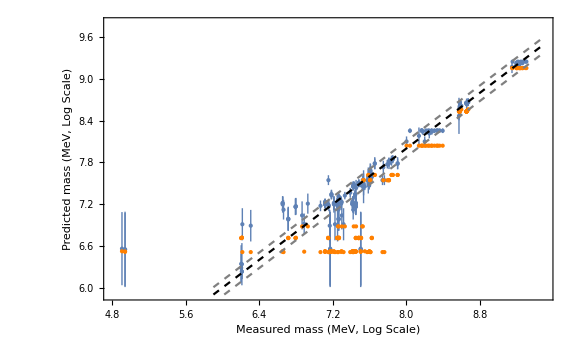

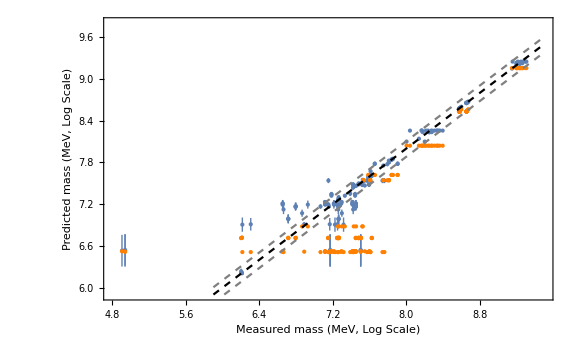

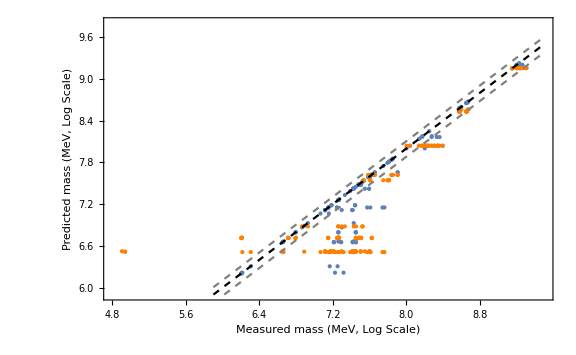

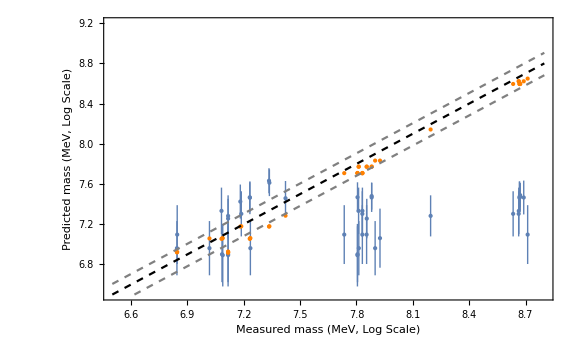

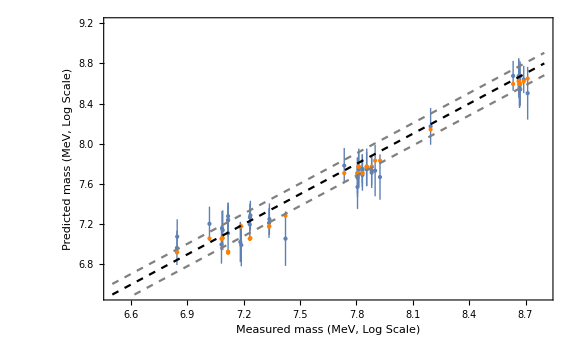

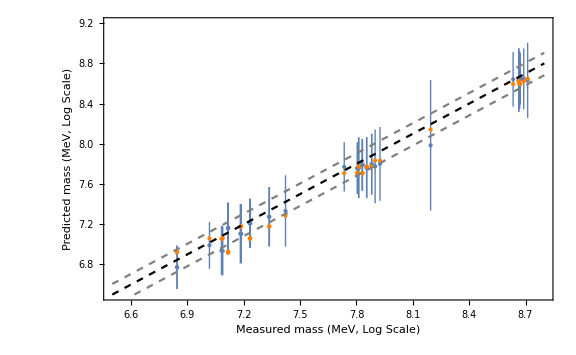

```mathematica
(*predictions for mesons *)
PR1={{4.8,9.5},{5.9,9.8}};
figA=funcPlotQM[MesonicData80,QmodelM,PR1]
fig1top=funcPlotQM[MesonicData100,QmodelM,PR1]
fig1bottom=funcPlotQM[M,QmodelM,PR1]

(*predictions for baryons *)
PR2={{6.5,8.8},{6.5,9.2}};
figB=funcPlotQM[BaryonicData80,QmodelB,PR2]
fig2top=funcPlotQM[BaryonicData100,QmodelB,PR2]
fig2bottom=funcPlotQM[B,QmodelB,PR2]
```